# Density data plotting code

## Version: 1.3.2

Common

## Directory setting

```mathematica
currentDir=NotebookDirectory[];
SetDirectory[currentDir];
expdir="../../data/density/";
simdir="../simulation/";
matdir="../../DFT code copy/DFFT-master/";
Needs["ErrorBarPlots`"]
```

## File import

### Experiment data

```mathematica
filename="a2021-07-28-02/data";
importdir=expdir;
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
```

```mathematica
imstack=hdf5File⟦1,9000;;18000⟧;
Histogram@imstack⟦;;,1,1⟧
```

```mathematica
imstack +=hdf5File⟦1,1;;18000⟧;
Histogram@imstack⟦;;,3,1⟧
```

### Simulation data

```mathematica
filename="meh";
importdir=simdir;
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
```

```mathematica
simstack=hdf5File⟦1,40000;;79999;;150,1,;;,;;⟧;
imstack=simstack;
Histogram@imstack⟦;;,3,1⟧
```

### Matlab data

```mathematica
"Trial_Data/occ_exp";
```

```mathematica
filename="osfstorage-archive/Figure 2/occ_rectangle_96flies";
importdir=matdir;
matFile=Import[ToString@Row@{importdir,filename,".mat"},"Data"]⟦1⟧;
```

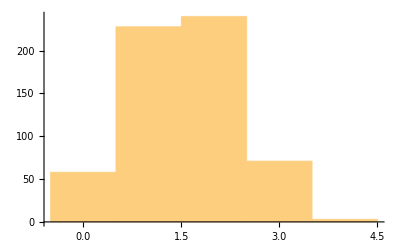

```mathematica
dim1=24;"Sqrt@Length@matFile⟦1⟧";
dim2=2;
imstack=Partition[#,dim1]&/@matFile;
Histogram@imstack⟦;;,-1,1⟧
```

```mathematica
timesteps=Length[imstack];
```

## Global Parameters

```mathematica
(* Normfactor is 1 if data is in counts; normfactor is Max[Total@Total] if data is in density*)
normfactor=1;
antcount=Round[normfactor Max[Total@Total@#&/@imstack]];
maxcount=Round[normfactor Max[imstack]];
```

## Decorrelation time

```mathematica
tau=150;
```

Simple average method

## Time integration

### Plot

```mathematica
(*imstack=imstack-Min[imstack];*)
squish=imstack⟦1⟧;
Do[
squish+=imstack⟦i⟧;
,{i,2,Length[imstack]}]
squish/=Length[imstack];
totalantness=antcount Length[imstack];
```

```mathematica
squished=(antcount squish)/(Total@Total@squish);
```

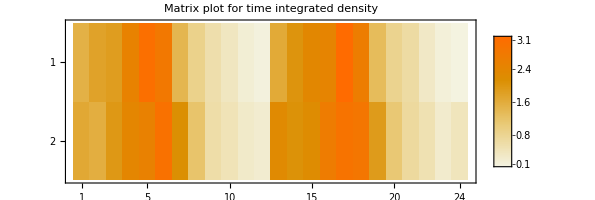

```mathematica
a=Show[MatrixPlot[squished,PlotLegends->Automatic,PlotLabel->"Matrix plot for time integrated density"]]
```

### Figure export

```mathematica
Export[ToString@Row@{filename,"out.png"},a];
```

```mathematica
(*antcount/Total[imstack⟦i⟧,{1,2}]*)
```

```mathematica
Directory[]
```

## Vexation

```mathematica
stackedimstack=imstack;
```

```mathematica
norm=ConstantArray[0,{dim2,dim1}];
```

```mathematica
Do[Do[
norm⟦j,k⟧=Sum[imstack⟦i,j,k⟧/antcount,{i,1,Length[imstack]}]
,{j,1,dim2}],{k,1,dim1}]
```

```mathematica
norm
```

{{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,0.893939,0.424242,0.151515,14.1212,17.4697,20.,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{14.1364,13.3333,16.7576,20.303,21.2121,26.0758,17.8788,8.69697,2.12121,1.21212,0.515152,0.484848,19.0909,17.6061,18.6364,22.6818,25.5,24.4848,16.3788,7.95455,2.63636,1.54545,0.5,0.969697}}

```mathematica
vexation=-Log[squished norm ];
```

```mathematica
prob=ConstantArray[0,{dim2,dim1}];
n=1;
```

```mathematica
Do[
Do[
prob⟦i,j⟧=Exp[-n vexation⟦i,j⟧]/(norm⟦i,j⟧ Factorial[n]);
,{i,1,dim2}],
{j,1,dim1}]
```

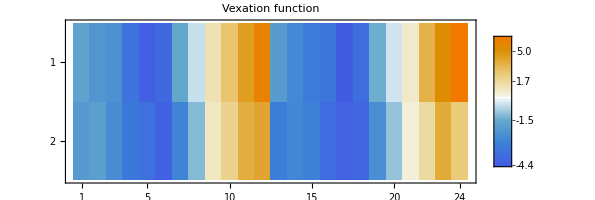

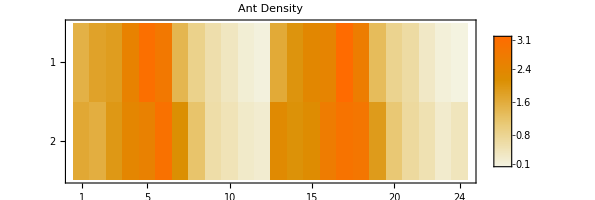

```mathematica
MatrixPlot[vexation,PlotLegends->Automatic,PlotLabel->"Vexation function"]
MatrixPlot[prob,PlotLegends->Automatic,PlotLabel->"Ant Density"]
```

## Symmetrify

```mathematica
halfa=vexation⟦1;;4⟧;
```

```mathematica
halfb=vexation⟦5;;8⟧;
```

```mathematica
MatrixPlot@Reverse[halfa]
```

```mathematica
halfsum=halfa+Reverse[halfb];
```

```mathematica
quartera=halfsum⟦;;,1;;4⟧;
quarterb=halfsum⟦;;,5;;8⟧;
```

```mathematica
quartersum=quartera+Reverse[quarterb,2];
```

```mathematica
unfold=ConstantArray[0,{8,8}];
```

```mathematica
Do[Do[
a=Mod[Abs[(-9Quotient[i,5])+Mod[i,5]],5];
b=Mod[Abs[(-9Quotient[j,5])+Mod[j,5]],5];
unfold⟦i,j⟧=quartersum⟦a,b⟧/4.
,{i,1,8}],
{j,1,8}]
```

```mathematica
halfa1=norm⟦1;;4⟧;
```

```mathematica
halfb1=norm⟦5;;8⟧;
```

```mathematica
MatrixPlot@Reverse[norm]
```

```mathematica
halfsum1=halfa1+Reverse[halfb1];
```

```mathematica
quartera1=halfsum1⟦;;,1;;4⟧;
quarterb1=halfsum1⟦;;,5;;8⟧;
```

```mathematica
quartersum1=quartera1+Reverse[quarterb1,2];
```

```mathematica
unfoldnorm=ConstantArray[0,{8,8}];
```

```mathematica
Do[Do[
a=Mod[Abs[(-9Quotient[i,5])+Mod[i,5]],5];
b=Mod[Abs[(-9Quotient[j,5])+Mod[j,5]],5];
unfoldnorm⟦i,j⟧=quartersum1⟦a,b⟧/4.
,{i,1,8}],
{j,1,8}]
```

```mathematica
MatrixPlot[unfold,PlotLegends->Automatic,PlotLabel->"Vexation symmetrized"]
```

```mathematica
prob=ConstantArray[0,{8,8}];
n=1;
```

```mathematica
Do[
Do[
prob⟦i,j⟧=Exp[-n unfold⟦i,j⟧]/(unfoldnorm⟦i,j⟧ Factorial[n]);
,{i,1,8}],
{j,1,8}]
```

```mathematica
MatrixPlot[prob,PlotLegends->Automatic,PlotLabel->"Density Symmetrized"]
```

## Frustration

```mathematica
(*Needs large number of ants*)
```

```mathematica
(*probf=HistogramList[timesquish,{0.001},"PDF"];*)
probf=HistogramList[normfactor Flatten@imstack,{0,13,1},"PDF"];
probf⟦1⟧=Drop[probf⟦1⟧,-1];
```

```mathematica
frustration[n_,pn_]:=-vexation n - Log[norm Factorial[n] pn];
```

```mathematica
ListPlot@(probfᵀ)
```

```mathematica
frustrray=ConstantArray[0,Length[probf⟦1⟧]];
Do[
frustrray⟦n⟧={probf⟦1,n⟧,Mean@Flatten@frustration[probf⟦1,n⟧,probf⟦2,n⟧]};
,{n,1,Length[frustrray]}]
```

```mathematica
ListPlot[frustrray,PlotLabel->"Frustration", AxesLabel->{"N","Frustration"}]
```

```mathematica
Module[
(* Set local parameters for plotting *)
{data=normfactor Flatten@imstack,
samplesize=0,
flatten=True,
axesLabel={"Number of ants","PDF"},
angularticks=True,
range, ticks, err, dist, hist, len, errors,
bincounts, binwidth, copy, temp},
bincounts=Ceiling@Max@data;
(* Modify structure of data and set up plotting parameters *)
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[0,Max[data],1],Automatic},
ticks=Automatic];
err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];

(* Generate basic plots using the configs *)
dist=SmoothKernelDistribution[data];
(* Generate histogrambins for further analysis *)
temp={};
hist=HistogramList[data,{Max[data]/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=Max[data]/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
coopy=hist;
hist=Partition[Riffle[histᵀ,errors],2];
(* Generate Error analysis and symmetry analysis plots *)
antcountErrorPlot=ErrorListPlot[hist,PlotRange->{{0,1.05(Max[data]+1)},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Ant count (With error bars)",PlotStyle->PointSize[0],Joined->True];
];
```

```mathematica
antcountErrorPlot
```

```mathematica
m=1;
frustprob=1/(m!)1/norm(Exp[-vexation]^m Exp[-frustrray⟦m,2⟧]);
```

```mathematica
MatrixPlot[frustprob,PlotLegends->Automatic]
```

## Hypothesis testing

### pseudo-free energy

```mathematica
pfe[b1_,b2_,n_]:=-Log[n!HistogramList[normfactor imstack⟦;;,b1,b2⟧,{-0.5,12.5,1},"PDF"]⟦2,n+1⟧];
```

```mathematica
ListPlot[Flatten[Table[{Range[0,12,1],pfe[i,j,Range[0,12,1]]}ᵀ,{i,1,dim2},{j,1,dim1}],1],PlotRange->Full,Joined->True,PlotLabel->"Pseudo-free energy vs N",AxesLabel->{"N_b","μ_b"}]
```

```mathematica
Module[
(* Set local parameters for plotting *)
{datastack=Flatten[Table[{Range[0,12,1],pfe[i,j,Range[0,12,1]]},{i,1,dim2},{j,1,dim1}],1],
samplesize=500,
axesLabel={"Number of ants","PDF"},
angularticks=True,
data,range,ticks,dist,len,errors,
bincounts, binwidth,plottable={}},
bincounts=Ceiling@Max@data;
Do[
data=datastack⟦n,2⟧;
(* Generate Horizontal error bars *)
range=datastack⟦n,1⟧;
(* Generate vertical error bars*)
errors={};
Do[
binwidth=range⟦2⟧-range⟦1⟧;
nnnn=binwidth;
AppendTo[errors,ErrorBar[0,Sqrt[Abs@data⟦i⟧(antcount-Abs@data⟦i⟧binwidth)/(samplesize binwidth)]]]
,{i,1,Length@data}];
AppendTo[plottable,{{range,data}ᵀ,errors}ᵀ],
{n,1,Length[datastack]}];
copy=plottable;
(* Generate Error analysis and symmetry analysis plots *)
pfeErrorPlot=ErrorListPlot[plottable⟦12;;28⟧,PlotRange->{{0,6},{-5,5}},AxesLabel->axesLabel,Frame->True,PlotLabel->"Histogram of Ant count (With error bars)",PlotStyle->PointSize[0],Joined->True]
(*mirror=[-copyᵀ⟦1⟧,Reverse[copyᵀ⟦2⟧];*)(*pfefrustrationErrorPlot=ListPlot[{{ -copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ,copy},PlotRange->{{0,Automatic},Full},PlotLabel->"Left-Right comparison for angular velocity distribution",PlotLegends->{"Left","Right"},ImageSize->700,Ticks->ticks,AxesLabel->{"Angular velocity (rad/s)", "PDF"},Joined->True];*)
];
pfeErrorPlot
```

```mathematica
check=HistogramList[normfactor imstack⟦;;,1,3⟧,{-0.5,12.5,1},"PDF"]⟦2⟧;
ListPlot[check,PlotRange->Full,PlotLabel->"Ant count distribution",Frame-> True, FrameLabel->{"Number of ants in a bin", "Probability"}]
```

```mathematica
(* Subscript[f, b] = -ln(N!P(N)) - Subscript[v, b] N - ln(Subscript[z, b]) *)
```

```mathematica
fN[i_,j_,n_]:=pfe[i,j,n]-( vexation⟦i,j⟧n+Log[ norm⟦i,j⟧]);
```

```mathematica
ListPlot[Flatten[Table[{Range[0,12,1],fN[i,j,Range[0,12,1]]}ᵀ,{i,1,dim2},{j,1,dim1}],1],Joined->False,PlotLabel->"Frustration from PFE vs N",AxesLabel->{"N_b","f_N_b"},PlotRange->{{0,6.1},{0,22}}]
```

$Aborted[]

Part::partw: Part {1,2,3,4,5,6,7,8,9,10,11,12,13} of {-0.5,12.5,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
filename="Trial_Data/vmle";
importdir=matdir;
vexcheck=Import[ToString@Row@{importdir,filename,".mat"},"Data"];
```

```mathematica
vexcheck=Partition[Flatten@vexcheck,24];
```

```mathematica
GraphicsColumn[{MatrixPlot[vexcheck,ImageSize->300,PlotLegends->Automatic,FrameTicks-> False],MatrixPlot[vexation,ImageSize->300,PlotLegends->Automatic,FrameTicks-> False]}]
```

```mathematica
Total@Total@vexcheck
```

```mathematica
Total@Total@vexation
```

```mathematica
Log@norm
```

```mathematica
vexation
```

```mathematica
vexcheck
```

Maximum Likelihood Estimation method (MLE)

```mathematica
(*
Outline.
Find the minimum of g(Vex,Frus)=-log(P(V,f|Data)), using preconditioned conjugate gradient. The arguments of g(V,F) at the minimum gives us the maximum likelihood estimates for the parameters used for the model. The values F(0) and F(1) are constrained at 0 so that the covariance matrix is non-singular, and there is asymptotic limit for distribution of estimators.
Source:
Pseudocode published by 
*)
```

## Function calls

### log-likelihood function g(x)

```mathematica
MyLogLikelihood[root_,hist_]:=Module[
{z,frust,vex,frustAV,nAV,loglikelihood},
frust=root⟦1;;maxcount+1⟧;
vex=root⟦maxcount+2;;maxcount+dim1 dim2+1⟧;
z=Table[Sum[Exp[-vex⟦b⟧(n-1)-frust⟦n⟧]/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
frustAV=Table[Sum[hist⟦n,b⟧,{n,1,maxcount+1}],{b,1,dim1 dim2}];
nAV=Table[Sum[hist⟦n,b⟧,{n,1,maxcount+1}],{b,1,dim1 dim2}];
loglikelihood=Sum[frustAV⟦b⟧+nAV ⟦b⟧vex⟦b⟧,{b,1,dim1 dim2}];
Return[loglikelihood]
];
```

### Log-Likelihood gradient function ∇g(x)

```mathematica
LogLikelihoodGradient[root_,hist_]:=Module[
{frust,vex,zmat,nmat,nAV,gradient,pmat},
frust=root⟦1;;maxcount+1⟧;
vex=root⟦maxcount+2;;maxcount+1+dim1 dim2⟧;
zmat=Table[Sum[Exp[-vex⟦b⟧(n-1)-frust⟦n⟧]/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
nmat=Table[1/zmat⟦b⟧Sum[(n Exp[-vex⟦b⟧(n-1)-frust⟦n⟧])/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
nAV=Table[Sum[hist⟦n,b⟧(n-1),{n,1,maxcount+1}],{b,1,dim1 dim2}];
gradient=ConstantArray[0,maxcount+1+dim1 dim2];
gradient⟦maxcount+2;;-1⟧=timesteps/tau(nAV-Mean[nmat]);
pmat=Table[Exp[-vex⟦b⟧(n-1)-frust⟦n⟧]/((n-1)!zmat⟦b⟧),{b,1,dim1 dim2},{n,1,maxcount+1}];
gradient⟦1;;maxcount+1⟧=Table[timesteps/tau Sum[hist⟦n,b⟧-pmat⟦b,n⟧,{b,1,dim1 dim2}],{n,1,maxcount+1}];
gradient⟦1⟧=0;
gradient⟦2⟧=0;
Return[gradient];
];
```

### Step size determination function

```mathematica
(*Performs a backtracking search to determine a 'sufficiently good' (according to the Armijo-Goldstein condition) step size to guarantee the function is eing minimized.*)
```

```mathematica
LineMin[root_,hist_,vecs_]:=Module[
{con1,con2,m,t,alpha,delta},
con1=0.0001;
con2=0.7;
m=(LogLikelihoodGradient[root,hist]. vecs)/Norm[vecs];
asdf=LogLikelihoodGradient[root,hist];
mm=m;
t=-con1 m;
alpha=0.001;
delta=MyLogLikelihood[root,hist]-MyLogLikelihood[root+alpha vecs/(Norm@vecs),hist];
add=alpha vecs/(Norm@vecs);
While[delta≤alpha t ,
alpha=alpha con2;
delta=MyLogLikelihood[root,hist]-MyLogLikelihood[root+alpha vecs/(Norm@vecs),hist];
];
Return[alpha]
];
```

### Covariance matrix calculation

```mathematica
GetCovMat[frust_,vex_,gauge_]:=Module[
{hessian=ConstantArray[0,{maxcount+1+dim1 dim2,maxcount+1+dim1 dim2}],gaugemat=ConstantArray[0,{maxcount+1+dim1 dim2,maxcount+1+dim1 dim2}],gtmat=ConstantArray[0,{maxcount+1+dim1 dim2,maxcount+1+dim1 dim2}],
eigenvalue,dims,covf1primevbprime,covf1primefnprime,redvectcorr,
zmat,pmat,nmat,n2mat,hessianFF,hessianVV,hessianVF,covmatp,covmatg,covmat,stderrors},
zmat=Table[Sum[Exp[-(n-1)vex⟦b⟧-frust⟦n⟧]/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
pmat=Table[Exp[-(n-1)vex⟦b⟧-frust⟦n⟧]/((n-1)!zmat⟦b⟧),{b,1,dim1 dim2},{n,1,maxcount+1}];
nmat=Table[1/zmat⟦b⟧Sum[((n-1)Exp[-(n-1)vex⟦b⟧-frust⟦n⟧])/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
n2mat=Table[1/zmat⟦b⟧Sum[((n-1)Exp[-(n-1)vex⟦b⟧-frust⟦n⟧])/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
hessianFF=Table[timesteps/tau KroneckerDelta[n,m]Sum[pmat⟦b,n⟧,{b,1,dim1 dim2}]-Sum[pmat⟦b,n⟧pmat⟦b,m⟧,{b,1,dim1 dim2}],{n,1,maxcount+1},{m,1,maxcount+1}];
hessianVV=Table[timesteps/tau KroneckerDelta[b,d](n2mat⟦b⟧-nmat⟦b⟧^2),{b,1,dim1 dim2},{d,1,dim1 dim2}];
hessianVF=Table[timesteps/tau pmat⟦b,n⟧(n-nmat⟦b⟧),{b,1,dim1 dim2},{n,1,maxcount+1}];
hessian⟦1;;maxcount+1,1;;maxcount+1⟧=hessianFF;
hessian⟦maxcount+2;;maxcount+1+dim1 dim2,maxcount+2;;maxcount+1+dim1 dim2⟧=hessianVV;
hessian⟦1;;maxcount+1,maxcount+2;;maxcount+1+dim1 dim2⟧=hessianVFᵀ;
hessian⟦maxcount+2;;maxcount+1+dim1 dim2,1;;maxcount+1⟧=hessianVF;
eigenvalue=Eigenvalues[hessian];
dims=Length[eigenvalue]-Count[1.Flatten[SetPrecision[DiagonalMatrix[eigenvalue]^5,1]],Except[0.]];
If[gauge==0,
(*True, zero gauge;*)
If[dims==2,
(*dims is zero*)
covmat=Inverse[hessian],
(*dims is not zero*)
covmat=ConstantArray[0,{maxcount+dim1 dim2+1,maxcount+dim1 dim2+1}];
covmat⟦dims+1;;-1,dims+1;;-1⟧=Inverse[hessian];
],
(*False -> Nonzero gauge; build gauge transformation matrix*)
gtmat=ConstantArray[0,{Length[hessian],Length[hessian]}];
gtmat⟦1;;maxcount+1,1;;maxcount+1⟧=Identity[maxcount+1];
gtmat⟦1;;maxcount+1,maxcount+2;;maxcount+1+dim1 dim2⟧=Outer[Times,Range[1+dims+maxcount+1],ConstantArray[1,dim1 dim2]]/(dim1 dim2);
gtmat⟦maxcount+2;;maxcount+1+dim1 dim2,maxcount+2;;maxcount+1+dim1 dim2⟧=ConstantArray[0,{dim1 dim2, dim1 dim2}];
gtmat⟦maxcount+2;;maxcount+1+dim1 dim2,1;;maxcount+1⟧=ConstantArray[1,{dim1 dim2, dim1 dim2}]/(dim1 dim2);
covmatp=Inverse[Hessian];
covmatg=gaugemat.covmat.gaugematᵀ;
covf1primevbprime=Sum[covmatp⟦maxcount+1;;-1,n⟧,{n,maxcount+1,Length[covmatp]}]/(dim1 dim2)+1/(dim1 dim2)^2 Sum[Sum[covmatp⟦m,n⟧,{n,maxcount+1,Length[covmatp]}],{m,maxcount+1,Length[covmatp]}];
covf1primefnprime=Sum[covmatp⟦maxcount+1;;-1,n⟧,{n,1,maxcount}]/(dim1 dim2)+Range[{3,maxcount}]1/(dim1 dim2)^2 Sum[Sum[covmatp⟦m,n⟧,{n,maxcount+1,Length[covmatp]}],{m,maxcount+1,Length[covmatp]}];
redvectcorr=Flatten[covf1primefnprime,covf1primevbprime,1];
If[dims==2,
(*dims is zero*)
covmat=ArrayFlatten[{{Total[covmatp⟦maxcount+1;;-1,maxcount;;-1⟧,2]/(dim1 dim2)^2,{redvectcorr}},{{redvectcorr}ᵀ,covmatg}}],

(*dims is not zero*)
covmat=ArrayFlatten[{{Total[covmatp⟦maxcount+1;;-1,maxcount;;-1⟧,2]/(dim1 dim2)^2,{redvectcorr}},{{redvectcorr}ᵀ,covmatg}}];
covmat=ArrayFlatten[{{ConstantArray[0,{dims-1,dims-1}],ConstantArray[0,{dims-1,Length[covmat]}]},{ConstantArray[0,{Length[covmat],dims-1}],covmat}}];
]
];
stderrors=Sqrt[Diagonal[covmat]];
Return[{covmat,stderrors}];
];
```

## Main routine

```mathematica
Module[{
flatstack=Flatten[#,1]&/@imstack,
(*The roots for guessing are initialized by random numbers*)
root=RandomReal[{0,1},{maxcount+1+dim2 dim1}],
(**)
hist=ConstantArray[0,{maxcount+1,dim2 dim1}],
ϵ=10^-7, (*Error tolerance for gradient*)
vecn=Range[0,maxcount],
sigfrust,sigvex,gauge=0,alpha,beta,delta,sigma,deltaold,m,s,rootold,stderror
},
Do[
Do[
Do[
If[flatstack⟦t,b⟧==n-1,
hist⟦n,b⟧=hist⟦n,b⟧+(1.flatstack⟦t,b⟧)/timesteps;]
,{t,1,timesteps}]
,{b,1,dim1 dim2}]
,{n,1,maxcount+1}];
root⟦1⟧=0;
root⟦2⟧=0;
(* Don't really know what the block below means, working on figuring it out *)
delta=-LogLikelihoodGradient[root,hist];
s=delta;
alpha= LineMin[root,hist,s];
rootold=root;
root=root+alpha delta;
m=0;
While[Norm[(root-rootold)/(maxcount+1+dim1 dim2)]≥ϵ,
m=m+1;
deltaold=delta;
delta=-LogLikelihoodGradient[root,hist];
beta=Norm[delta]^2/Norm[deltaold]^2;
s=delta+beta s;
alpha= LineMin[root,hist,s];
root=root+alpha s;
rootold=root;
root⟦1⟧=0;
root⟦2⟧=0;
];
If[
(*Condition*)
gauge==0,
(*True*)
frustration=root⟦1;;maxcount+1⟧;
vexation=root⟦maxcount+2;;maxcount+1+dim1 dim2⟧;
{sigma,stderror}=GetCovMat[frustration,vexation,gauge],
(*False*)
frustration=root⟦1;;maxcount+1⟧+vecn/(dim1 dim2)Sum[root⟦j⟧,{j,maxcount+2,maxcount+dim1 dim2}];
vexation=root⟦maxcount+2;;maxcount+1+dim1 dim2⟧-1/(dim1 dim2)Sum[root⟦j⟧,{j,maxcount+2,maxcount+1+dim1 dim2}];
{sigma,stderror}=GetCovMat[frustration,vexation,gauge];
];
asigfrust=Diagonal[sigma]⟦1;;maxcount⟧;
asigvex=Diagonal[sigma]⟦maxcount+2;;maxcount+dim1 dim2⟧;
]
```

## Prediction

```mathematica
Module[
{ϵ=10^-7.,
count=0,
maxsteps=130,
delta,mu,mustar,a,b,nwiggle
},
mu=Max[vexation];
nwiggle=0;
delta=Abs[Max@vexation - Min@vexation];
a=mu+2delta;
b=mu-2delta;
mustar=0;
While[count≤maxsteps,
mu=(a+b)/2;
zmat=Table[Sum[Exp[-(n-1)vexation⟦n⟧-frustration⟦n⟧]/((n-1)!),{n,1,maxcount+1}],{b,1,dim1 dim2}];
nexp=Table[Sum[((n-1)Exp[-(n-1)vexation⟦n⟧-frustration⟦n⟧])/((n-1)!zmat⟦b⟧),{n,1,maxcount+1}],{b,1,dim1 dim2}];
nwiggle=Sum[nexp⟦b⟧,{b,1,dim1 dim2}];
If[
Abs[nwiggle-nhat]≤ϵ,
mustar=mu;
];
c+=1;
If[nwiggle<nhat,
b=mu,
a=mu];
];
Return[mu,nexp];
]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

$Aborted

```mathematica
({1,2,3}//MatrixForm).({{1,2,3}}//MatrixForm)
```

```mathematica
Outer[Times,{1,2,3},{1,2,3}]
```

```mathematica
a={{1,2},{1,2}};
```

```mathematica
Flatten[{{a,a},{a,a}},2]//MatrixForm
```

```mathematica
Total[a,1]
```

```mathematica
b=1;
```

```mathematica
c={1,1,1};
d={c,c,c};
```

```mathematica
{ArrayFlatten[{b,c},1],ArrayFlatten[{{c}ᵀ,d},1]}//MatrixForm
```

```mathematica
Join
```

```mathematica
ArrayFlatten[{{b,{c}},{{c}ᵀ,d}}]//MatrixForm
```

```mathematica
c.c
```

3

```mathematica
asdf={1,2,3,4,5,0.};
```

```mathematica
DeleteCases[asdf,0];
DeleteCases[asdf,0.]
```

{1,2,3,4,5}

```mathematica
Count[asdf,Except[0.]]
```

5